```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
k=Flatten[Import["./k.dat"]];
b1=Partition[Flatten[Import["./bk.dat"]],51];
a1=Partition[Flatten[Import["./ak.dat"]],51];
(*lam1dl=lam1[[1;;Length[k]]](**k^-2*);*)
```

```mathematica
Show[ListPlot[Transpose[{k,lam1dl}],PlotRange->All(*{{10^-5,1000},{-0.7,0.5}}*),ScalingFunctions->{"Log",Automatic}]]
```

Transpose::nmtx: {{700.,699.92068898260735507235767793079787,699.83797510513450641179488504081333,699.74200686786595320535466907178482,699.64484545538410280656582513136566,699.56965843420303401608467842926691,«39»,695.57706597879112939296374614547348,695.45056966860373886675988497967198,695.32248946875036460491492982705002,695.19297554245643411050730169588857,695.06228126564436853110561515860943,«724»},{«59»}} 的前两层无法转置.

Transpose::nmtx: {{700.,699.9206889826074,699.8379751051345,699.742006867866,699.6448454553841,699.569658434203,699.4864997738631,699.395525660404,699.2968086480163,«33»,695.9463033761344,695.8249776236349,695.7018871056233,695.5770659787911,695.4505696686037,695.3224894687504,695.1929755424564,695.0622812656444,«724»},«1»} 的前两层无法转置.

Transpose::nmtx: {{700.,699.921,699.838,699.742,699.645,699.57,699.486,699.396,699.297,699.19,699.076,698.96,698.847,698.739,698.643,698.547,698.437,698.346,698.241,«14»,696.803,696.724,696.642,696.55,696.461,696.379,696.284,696.18,696.066,695.946,695.825,695.702,695.577,695.451,695.322,695.193,695.062,«724»},{«23»}} 的前两层无法转置.

General::stop: 在本次计算中，Transpose::nmtx 的进一步输出将被抑制.

ListPlot::lpn: {{700.,699.9206889826074,699.8379751051345,699.742006867866,699.6448454553841,«42»,695.3224894687504,695.1929755424564,695.0622812656444,«724»},{«39»}}^T 不是由数字或者数对组成的列表.

Show::gtype: ListPlot 不是一个图形类别.

```mathematica
Dimensions[b1]
```

{309,51}

```mathematica
39474/51
```

774

```mathematica
Length[k]
```

309

```mathematica
b1[[3]]
```

{1.2171610283952803310104882908767056×10^6,640642.97616285456496459481705626679,532345.27575664186741055360086523063,481158.06252764198070403832057334615,417602.64298545447512342185603822545,347997.94532556829899182359280734451,278395.18055635472435107160189348916,213766.00594825132487169037604314206,157511.14593744221181836967081343839,111344.00537732853420012035160971415,75487.467190324997935924833060687186,49066.668046006413908839165907469989,30565.716282414011063997518082167701,18240.365350105438959233652867378999,10422.760630864177132311643051510621,5699.9575442736589581880856003203677,2981.8621628768715012908392100978284,1491.496110381501795208588643512666,712.94989675906787206075626498159503,325.4610143480982886423592296467227,141.6868642778251067355007608457736,58.623312587508059918058414150757959,22.873390343246374984640435596261981,8.2868984789777777421019307187957258,2.7270067982802331547266927796782418,0.82162786351726160501803494192754611,0.28680787581904477900902698386216331,0.1873795527146199268507917570792254,0.16916038841411369629366568750652022,0.12617753613183878522775954251638631,0.056646626225262810577074309003388923,-0.010477238400044999324972223909775141,-0.049011158473352642642079579086397489,-0.051945486930302826466307150367618529,-0.028361722414613994529827440786418268,0.0030643453272999957746948351431636635,0.026528619749856492965079142740944207,0.03334248788510621887606929358406113,0.025410291661226891606104141738850919,0.0096744791805073518971945422357374024,-0.0045466201263741119543981853298912834,-0.011995145933688605114969958458840443,-0.010861678067827689837845646431917175,-0.0043705629880101567234618527330594774,0.0037417272634179981659074205758630632,0.0091965740938528250624938296264847233,0.010897147925114743345076791731605882,0.008746051957002617057056124020387272,0.0051663929020481048279506902855758467,0.0016143939062519884200894547331041963,0.}

```mathematica
a1[[1]]
```

{9.3810717201731072071335078534031417×10^9,5.1364747256599114702634162303664922×10^9,5.9795935687183903399562336387434562×10^8,2.8683111565751388310137843586387433×10^8,2.4964930436857756769469895287958116×10^8,2.087976000173553946130562827225131×10^8,1.6778378572823189940128026832460734×10^8,1.2951730828144267217026955170157069×10^8,9.6021452691414218922560127617801047×10^7,6.835425445829497332348249345549739×10^7,4.6708740546501319445864692408376964×10^7,3.0628682325574829940396453697643981×10^7,1.9266429204797078177566927765052359×10^7,1.1621020790194878403428961469240839×10^7,6.7184026443314352584758978239528803×10^6,3.7209614645528581129942888988874346×10^6,1.9732371402930099302561495316590315×10^6,1.001344220447250685766729384816754×10^6,485946.45992277601626530991798920158,225366.47416723788720775025053174086,99805.152845480913267085689524705504,42171.191343086693650452878462706564,16985.618735479527392000428044983232,6515.0318436528609685248729446171472,2377.1062132601622560339448339652019,824.06348719973609592590032447695107,271.07351556263039838181350243653302,84.490446518915061212963965862833397,24.913849589851985353956983975715038,6.9380340615477581333682301858956907,1.8212339089374380538265064787802273,0.44968739942620670562830975484005446,0.10419581058474134765531682148478262,0.022596655770522435663157649806344697,0.0045731114012538829187052448600754925,0.00086085698177257293685066002362111526,0.00015020502810179589140990700672097359,0.000024091946914701253867082692779806635,3.5593941627979080136760581486914485×10^-6,4.6281085046905410720758753058506987×10^-7,5.3480714054213981874857538164456817×10^-8,9.3989839168143847179351297605796527×10^-11,1.2154470909872210922337740631174071×10^-8,-3.1954304735225307566534184719856841×10^-8,-1.9817710383648482125868712870107514×10^-8,2.2051515731172173217055173568429203×10^-8,3.011757448671174703388969226561899×10^-9,4.5692866743362242310985186698823329×10^-8,-1.6719359143413435322609408603663396×10^-8,-6.1330475519122336889258580779097062×10^-8,1.4761121395758951495162639511927327×10^-9}

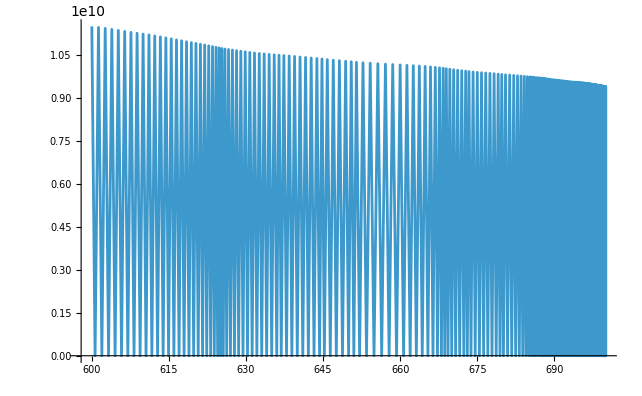

```mathematica
ListLinePlot[Transpose[{k,Transpose[a1][[1]]}]]
```